# Late time approaches to the Hubble tension deforming H(z), worsen the growth tension - G. Alestas and L. Perivolaropoulos - Figure 1, 4

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb,NMinimize::cvmit,NIntegrate::slwcon];
Needs["ErrorBarPlots`"];
```

### Various Constants

```mathematica
(* TT,TE,EE+lowE Likelihoods - 4th column of arxiv:1807.06209 *)
H0pl=67.4;
h0pl=H0pl/100;
(* Planck values as given in 1502.01589 (Table 3, column 4) *)
ompl=0.315;
σ8pl=0.831;
obh2=0.0224;
orh2=(1+3.046*7/8*(4/11)^(4/3))2.473*10^(-5);
omh2=ompl h0pl^2;
h0r=0.7403;
(* Other Constants *)
Tcmb=2.7255;
c=299792.458;
cH0=2997.92458;
(* Dashing Options *)
d1=.025;
d2=.001;
w0min=-18;
w0max=-0.5;
```

### Calculation of z_rec and Ω_(0m) Theoretical

```mathematica
(* See Eq. (E-1) from arxiv:9510117 *)
zrec[om_,obh2_,h_]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(om h^2)^(0.560/(1+21.1(obh2)^1.81)));
zrec=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(omh2)^(0.560/(1+21.1(obh2)^1.81)));
(* Find the Subscript[Ω, 0m] Theoretical from the Planck18/ΛCDM Value *)
eqomth=om*h^2==0.1432;
omth=Solve[eqomth/. h->h0r,om]
```

SetDelayed::write: Tag Real in 1091.87[om_,obh2_,h_] is Protected.

{{om→0.261293}}

## Section III - Growth of Perturbations and the Growth Tension in Hubble Deformation Models

## χ^2 Calculations for LwPT DE model - Figure 3

#### CMB Data

```mathematica
(* Central values for {R, Subscript[l, a], Subscript[Ω, b] h^2} from Planck18/ΛCDM - See Eq. (31) on page 7 of arxiv:1811.07425 *)
datacmb={1.74963,301.80845,0.02237};
(* Inverse Covariance Matrix using  for {R, Subscript[l, a], Subscript[Ω, b] h^2} *)
covcmb=10^-8({{1598.9554, 17112.007, −36.311179}, {17112.007, 811208.45, −494.79813}, {-36.311179, -494.79813, 2.1242182}});
invcovcmb=Inverse[covcmb];
```

#### BAO Data

```mathematica
datadvpltmgcosmomc={{0.106,439.3,19.6},{0.44,1716,83},{0.60,2221,100},{0.73,2516,86},{0.15,664,25},{0.32,1270,14},{0.57,2033,21},{0.38,1477,16},{0.51,1877,19},{0.61,2140,22}};
datadvpltmathematica={{0.106,439.3,19.6},{0.44,1716,83},{0.60,2221,100},{0.73,2516,86},{0.15,664,25},{0.57,2033,21},{0.61,2140,22}};
(* Full List of BAO Dv Data from https://arxiv.org/pdf/1812.05356.pdf *)
datadvall={{0.978,2933.59,327.71},{1.23,3522.04,192.74},{1.526,3954.31,141.71},{1.944,4575,241.61},{1.52,3985.2,162.36},{0.72,2353,62},{0.35,1356,25},{0.106,439.3,19.6},{0.15,664,25},{0.38,1477,16},{0.51,1877,19},{0.61,2140,22},{0.32,1270,14},{0.57,2033,21},{0.44,1716,83},{0.60,2221,100},{0.73,2516,86},{1.52,3843,147},{0.31,1208.36,33.81},{0.36,1388.36,55},{0.4,1560.06,40},{0.44,1679.88,35},{0.48,1820.44,39},{0.52,1913.54,47},{0.56,2001.91,51},{0.59,2100.43,48},{0.64,2207.51,55},{0.275,1061.87,29}};
```

```mathematica
(* 6dFGs and WiggleZ BAO data - See arxiv:1605.02702 on page 6 *)
databao={{0.106,0.336,0.015},{0.44,0.073,0.031},{0.6,0.0726,0.0164},{0.73,0.0592,0.0185}};
Cijbaoinv=({{1/databao[[1,3]]^2, 0, 0, 0}, {0, 1040.3, -807.5, 336.8}, {0, -807.5, 3720.3, -1551.9}, {0, 336.8, -1551.9, 2914.9}});
```

```mathematica
(*(Dv/rs)- arxiv:1409.3242 and (Dv/rs)- arxiv:1312.4877 *)
dataSDSS={{0.15,4.465666824,0.1681350461},{0.32,8.62,0.15},{0.57,13.70,0.12}};
```

```mathematica
(* BAO measurements from Lya are {Da/rs, DH/rs} - arxiv:1904.03400 *)
dataLya={{2.34,11.28,0.65},{2.34,9.18,0.28}};
CijLyainv=({{1/dataLya[[1,3]]^2, 0}, {0, 1/dataLya[[2,3]]^2}});
vecLya[om_,obh2_,w0_,wa_,h_,at_]:={dataLya[[1,2]]-DA[dataLya[[1,1]],om,w0,wa,h,at]/rs[zdrag,om,obh2,w0,wa,h,at],dataLya[[2,2]]-DH[dataLya[[2,1]],om,w0,wa,h,at]/rs[zdrag,om,obh2,w0,wa,h,at]};
(* Total length of BAO datapoints *)
ndatBAO=Length[dataSDSS]+Length[databao]+Length[dataLya];
```

#### Full Pantheon Data

```mathematica
(* Import the Full Pantheon Data *)
dataPanth=Import[".\\data\\lcparam_full_long_zhel.txt","Table"];
ndatPanth=Length[dataPanth]-1;
Dij0=Import[".\\data\\sys_full_long.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Id=ConstantArray[1,ndatPanth];
(* Statistical Uncertainties *)
Covstat=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2];
(* Systematic Uncertainties *)
Covsys=Dij;
Cijtot=Covsys+Covstat;
InvCovTotal=Inverse[Cijtot];
InvCovstat=Inverse[Covstat];
```

### Total χ^2 for ΛCDM and wCDM Models

```mathematica
(* Use this cell in order to avoid the (time-consuming) best fit acquisition process *)
minlcdm={1574.2432412,{1041.9139560469093,{om->0.3135537205040999,h->0.6745882574431542}}}
minwcdm={943.9898863,{1039.3580852154394,{om->0.3108665736514824,h->0.6796064032840277,w0->-1.0286031364696788}}}
```

{1574.24,{1041.91,{om→0.313554,h→0.674588}}}

{943.99,{1039.36,{om→0.310867,h→0.679606,w0→-1.0286}}}

## CPL Dark Energy Model

#### χ^2 Analysis for CPL Dark Energy Model

```mathematica
(* nCPL Dark Energy Model as a function of α *)
wcpl[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
(* Subscript[f, DE](α) for nCPL Dark Energy Model *)
fcpl[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a])
(* See Eq. (2) of arxiv:9709112 *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
Hcpl[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))fcpl[a,w0,wa,n]]
(* Comoving sound horizon at drag redshift *)
rscpl[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[x,obh2]/(x^2Hcpl[x,om,w0,wa,n,h]),{x,10^-11,1/(1+ze[om,obh2,h])}]
cs[a_?NumberQ,obh2_?NumberQ]:=c/√(3(1+(31500 obh2(Tcmb/2.7)^-4)a));
(* Redshift at decoupling - See Eqs. (66)-(68) of arxiv:0803.0547 *)
zcmb[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(om h^2)^(0.560/(1+21.1(obh2)^1.81)))
(* Drag redshift - see Eq. (4) of arxiv:9709112 *)
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om h^2)^0.251)/(1+0.659 (om h^2)^0.828)(1+(0.313(om h^2)^-0.419(1+0.607(om h^2)^0.674))(obh2)^(0.238(om h^2)^0.223))
Clear[DLsolcpl,DLcpl,dLcpl]
DLsolcpl[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(DLsolcpl[om,w0,wa,n,h]=NDSolve[{D[dLcpl[zz]/(1+zz),zz]==1/(Hcpl[1/(1+zz),om,w0,wa,n,h]/(100h)),dLcpl[0]==0},dLcpl,{zz,0,1300},MaxSteps->Infinity])
DLcpl[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(c/(100h)dLcpl[z]/.DLsolcpl[om,w0,wa,n,h])[[1]]//Chop
(* Angular diameter distance with curvature, see arxiv:0803.0547  *)
DAcpl[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=1/(1+z)^2 DLcpl[z,om,w0,wa,n,h]
baodacpl[z_,om_,w0_,wa_,n_,h_]:= DAcpl[z,om,w0,wa,n,h](rscpl[zdrag,om0pl,obh2,-1,0,1,h0pl]/rscpl[zdrag,om,obh2,w0,wa,n,h]);
(* Dilation scale *)
Dvcpl[zbao_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((DLcpl[zbao,om,w0,wa,n,h]/(1+zbao))^2  (c*zbao)/Hcpl[1/(1+zbao),om,w0,wa,n,h])^(1/3)
(* BAO Subscript[d, z] ratio *)
dzcpl[zbao_,om_,obh2_,w0_,wa_,n_,h_]:=rscpl[zdrag,om,obh2,w0,wa,n,h]/Dvcpl[zbao,om,w0,wa,n,h]
(* DH "distance" *)
DHcpl[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=c/Hcpl[1/(1+z),om,w0,wa,n,h]
hzcpl[z_,om_,w0_,wa_,n_,h_]:=Hcpl[1/(1+z),om,w0,wa,n,h]
baodvcpl[z_,om_,w0_,wa_,n_,h_]:=rscpl[zdrag,om0pl,obh2,-1,0,1,h0pl]/dzcpl[z,om,obh2,w0,wa,n,h];

(* Scaled distance at recombination *)
Rcpl[om_,obh2_,w0_,wa_,n_,h_]:=√(om (100h)^2)DAcpl[zcmb[om,obh2,h],om,w0,wa,n,h](1+zcmb[om,obh2,h])/c
(* Angular scale of sound horizon at recombination *)
lacpl[om_,obh2_,w0_,wa_,n_,h_]:=π (DAcpl[zcmb[om,obh2,h],om,w0,wa,n,h](1+zcmb[om,obh2,h]))/(rscpl[zcmb,om,obh2,w0,wa,n,h])
```

#### CMB χ^2

```mathematica
(* χ^2 for R *)
veccpl[om_,obh2_,w0_,wa_,n_,h_]:={Rcpl[om,obh2,w0,wa,n,h]-datacmb[[1]],lacpl[om,obh2,w0,wa,n,h]-datacmb[[2]],obh2-datacmb[[3]]};
chi2Rcpl[om_,obh2_,w0_,wa_,n_,h_]:=veccpl[om,obh2,w0,wa,n,h].invcovcmb.veccpl[om,obh2,w0,wa,n,h]
```

#### BAO χ^2

```mathematica
(* 6dFGs and WiggleZ BAO data, see arxiv:1605.02702 *)
vecbaocpl[om_,obh2_,w0_,wa_,n_,h_]:=Table[(databao[[i,2]]-dzcpl[databao[[i,1]],om,obh2,w0,wa,n,h]),{i,1,Length[databao]}];
(* BAO measurements from Lya are {Da/rs, DH/rs} - arxiv:1904.03400 *)
vecLyacpl[om_,obh2_,w0_,wa_,n_,h_]:={dataLya[[1,2]]-DAcpl[dataLya[[1,1]],om,w0,wa,n,h]/rscpl[zdrag,om,obh2,w0,wa,n,h],dataLya[[2,2]]-DHcpl[dataLya[[2,1]],om,w0,wa,n,h]/rscpl[zdrag,om,obh2,w0,wa,n,h]};
(* Total BAO chi^2 *)
chi2baocpl[om_,obh2_,w0_,wa_,n_,h_]:=vecbaocpl[om,obh2,w0,wa,n,h].Cijbaoinv.vecbaocpl[om,obh2,w0,wa,n,h]+Sum[(dataSDSS[[i,2]]-1/dzcpl[dataSDSS[[i,1]],om,obh2,w0,wa,n,h])^2/dataSDSS[[i,3]]^2,{i,1,Length[dataSDSS]}]+vecLyacpl[om,obh2,w0,wa,n,h].CijLyainv.vecLyacpl[om,obh2,w0,wa,n,h]
```

#### Full Pantheon χ^2

```mathematica
(* χ^2 Formula for Full Pantheon Data *)
chi2Panthcpl[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ]:=
Module[{Δm},
Δm=Table[dataPanth[[1+i,5]]-(M+5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DLcpl[dataPanth[[1+i,2]],om,w0,wa,n,h0r]]+25),{i,1,ndatPanth}];
Δm.InvCovTotal.Δm]
```

```mathematica
chi2Panthcplplanck[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ]:=
Module[{Δm},
Δm=Table[dataPanth[[1+i,5]]-(M+5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])DLcpl[dataPanth[[1+i,2]],om,w0,wa,n,h0pl]]+25),{i,1,ndatPanth}];
Δm.InvCovTotal.Δm]
```

#### Total χ^2 for CPL Dark Energy Model

```mathematica
(* Construct the Total χ^2 as a sum of the individual χ^2 *)
chi2totalcpl[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=chi2Rcpl[om,obh2,w0,wa,1,h]+chi2baocpl[om,obh2,w0,wa,1,h]+ chi2Panthcpl[M,om,w0,wa,1]
chi2totalcplplanck[M_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,h_?NumberQ]:=chi2Rcpl[om,obh2,w0,wa,1,h]+chi2baocpl[om,obh2,w0,wa,1,h]+ chi2Panthcplplanck[M,om,w0,wa,1]
```

### Import the Growth Data

```mathematica
(* Import the Robust Growth Data from https://arxiv.org/pdf/1806.10822.pdf*)
datagrowth=Import[".\\data\\data_growth_2018_main.txt","Table"];
```

### Growth Data Analysis - CPL

```mathematica
dchi[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsig[dchi1_]:=FindRoot[dchi[nsig1]==dchi1,{nsig1,1}][[1,2]]
dchi2[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsig2[dchi1_]:=FindRoot[dchi2[nsig1]==dchi1,{nsig1,3}][[1,2]]
```

```mathematica
(* Add support for WiggleZ and SDSS data Cij *)
Cijwigglez=Import[".\\data\\Cij_WiggleZ.txt","Table"];
Cijsdss=Import[".\\data\\Cij_SDSS.txt","Table"];
```

```mathematica
wcpl[z_,w0_,w1_]:=w0+w1 z/(z+1)
decpl=Exp[3 Integrate[(1+wcpl[zp,w0,w1])/(1+zp),{zp,0,z},Assumptions->z>0]];
Hcpl[z_,h_,w0_,w1_]:=√(omh2 (1+z)^3+orh2  (1+z)^4+(h^2 -omh2-orh2 )ⅇ^(3 (-(w1 z)/(1+z)+(1+w0+w1) Log[1+z])))
comdz[zmax_?NumberQ,hh_,w0_,w1_]:=NIntegrate[1/Hcpl[z,hh,w0,w1],{z,0,zmax}];
```

```mathematica
(* For given w0 what is the w1 that addresses the Hubble tension (consistent with CMB and Hcpl[0]=h0r) *)
```

```mathematica
w1ht[w0_]:=Part[FindRoot[comdz[zrec,h0r,w0,w1]==comdz[zrec,h0pl,-1,0],{w1,0}],1,2]//Chop
```

```mathematica
amin=0.001;
dsol[h0_?NumberQ,w0_?NumberQ,w1_?NumberQ]:=(dsol[h0,w0,w1]=Module[{a},NDSolve[{-((3 omh2 d[a])/(2 a^5  Hcpl[1/a-1,h0,w0,w1]^2))+d'[a] (3/a+D[Hcpl[1/a-1,h0,w0,w1],a]/Hcpl[1/a-1,h0,w0,w1])+d''[a]==0,d[amin]==amin,d'[amin]==1},d,{a,amin,1}][[1]]])
Da[a_?NumberQ,h0_?NumberQ,w0_?NumberQ,w1_?NumberQ]:=d[a]/.dsol[h0,w0,w1]
```

```mathematica
grtab=Table[{Da[1,h0r,-1+dw0,w1ht[-1+dw0]]/Da[1,h0pl,-1,0],-1+dw0,w1ht[-1+dw0],-1+dw0+w1ht[-1+dw0]},{dw0,-1,1,0.01}];
```

```mathematica
fa[aa_,h0_,w0_,wa_]:=a d'[a]/d[a]/.a->aa/.dsol[h0,w0,wa]
fσ8[a_?NumberQ,h0_?NumberQ,w0_?NumberQ,wa_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,h0,w0,wa])/Da[1,h0,w0,wa] fa[aa,h0,w0,wa]/.aa->a
fσ8z[z_?NumberQ,h0_?NumberQ,w0_?NumberQ,wa_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,h0,w0,wa])/Da[1,h0,w0,wa] fa[aa,h0,w0,wa]/.aa->1/(1+z)
Da[1,h0pl,-1,0]
```

0.708858

```mathematica
Wigglez={13,14,15};
SDSS={19,20,21,22};
Cijfs81=DiagonalMatrix[datagrowth[[All,3]]^2];
Cijfs81[[Wigglez,Wigglez]]=Cijwigglez;
Cijfs81[[SDSS,SDSS]]=Cijsdss;
InvCijfs81=Inverse[Cijfs81];
(*Fiducial correction from robust paper*)
omf={0.3,0.3,0.266,0.3,0.31,0.3,0.27,0.27,0.25,0.25,0.274,0.307115,0.27,0.27,0.27,0.3,0.3,0.27,0.31,0.31,0.31,0.31};
```

```mathematica
(* χ^2 correlated term *)
vecgr[data_,w0_,wa_,h0_,σ8_]:=Table[data[[i,2]]-fσ8[1/(1+data[[i,1]]),h0,w0,wa,σ8],{i,1,Length[data]}]
chi2corr[data_,w0_,wa_,h0_,σ8_]:=vecgr[data,w0,wa,h0,σ8].InvCijfs81.vecgr[data,w0,wa,h0,σ8]
```

```mathematica
(* Planck Value for Subscript[σ, 8] *)
fmins8pl=FindMinimum[chi2corr[datagrowth,-1,0,om,σ8pl],{om,.3,.31}]
```

{12.4129,{om→0.779162}}

```mathematica
(* Minimize χ^2 over different parameters *)
fmwc=FindMinimum[chi2corr[datagrowth,-1,0,h0pl,σ8],{σ8,.8,.81}]
fmwc3=FindMinimum[chi2corr[datagrowth,-1.5,1.08,h0r,σ8],{σ8,.8,.81}]
fmwc4=FindMinimum[chi2corr[datagrowth,-1.73,1.72,h0r,σ8],{σ8,.8,.81}]
fmwc5=FindMinimum[chi2corr[datagrowth,-1.22,0,h0r,σ8],{σ8,.8,.81}]
σ8bfwc=fmwc[[2,1,2]];
σ8bfwc3=fmwc3[[2,1,2]];
σ8bfwc4=fmwc4[[2,1,2]];
σ8bfwc5=fmwc5[[2,1,2]];
```

{13.6535,{σ8→0.750709}}

{13.0787,{σ8→0.757868}}

{13.62,{σ8→0.744217}}

{12.6523,{σ8→0.769323}}

```mathematica
cpls8winfty={};
Do[fms8winfty=FindMinimum[chi2corr[datagrowth,grtab[[i,2]],grtab[[i,3]],h0r,σ8],{σ8,.8,.81}];
AppendTo[cpls8winfty,{grtab[[i,2]]+grtab[[i,3]],fms8winfty[[2,1,2]]/fmwc[[2,1,2]]}],{i,1,Length[grtab]}]
```

```mathematica
cpls8winfty;
```

```mathematica
(*cpldgnchi2={};
Do[
chi2cpldgn=NMinimize[{chi2totalcpl[M,omth[[1,1,2]],grtab[[i,2]],grtab[[i,3]],h0r],-19.8<M<-19},{M},WorkingPrecision->10]//AbsoluteTiming;
dchicpldgn=chi2totalcpl[chi2cpldgn[[2,2,1,2]],omth[[1,1,2]],grtab[[i,2]],grtab[[i,3]],h0r]-minlcdm[[2,1]];
AppendTo[cpldgnchi2,{dchicpldgn,grtab[[i,2]],grtab[[i,3]],grtab[[i,2]]+grtab[[i,3]]}];
If[Mod[i,3]==0,Print["Finished step ",i," of ",Length[grtab], " realizations"]],{i,1,Length[grtab]}]
(* The results of the Do loop *)
cpldgnchi2*)
```

```mathematica
(* Use this cell in order to avoid the (time-consuming) best fit acquisition process *)
cpldgnchi2={{943620.1946880063,-2.,2.2420871088386054,0.2420871088386054},{781765.1388019946,-1.99,2.22592907429005,0.23592907429004994},{643598.2682628562,-1.98,2.2096448628273424,0.22964486282734242},{526376.6465764038,-1.97,2.1932265540983913,0.22322655409839132},{427560.4445211246,-1.96,2.1766656587010615,0.21666565870106158},{344814.07058462757,-1.95,2.1599530822833084,0.20995308228330845},{276005.0018403433,-1.94,2.1430790898725394,0.20307908987253942},{219200.33465319383,-1.93,2.126033271300062,0.1960332713000621},{172661.1880308894,-1.92,2.1088045088385927,0.1888045088385928},{134835.17760300275,-1.9100000000000001,2.0913809484669144,0.18138094846691422},{104347.26329217528,-1.9,2.073749976515487,0.17374997651548707},{79989.23786667036,-1.8900000000000001,2.0558982038250324,0.1658982038250323},{60708.25940888091,-1.88,2.0378114599560195,0.15781145995601964},{45594.73854227136,-1.87,2.01947482389525,0.1494748238952499},{33869.62519321809,-1.8599999999999999,2.0008725301247474,0.14087253012474754},{24872.216568517048,-1.85,1.981988247119585,0.131988247119585},{18047.307416446176,-1.8399999999999999,1.9628049097419882,0.12280490974198832},{12933.326690318514,-1.83,1.9433049316769608,0.11330493167696076},{9150.612066552836,-1.82,1.9234703079229953,0.10347030792299527},{6390.675026785172,-1.81,1.9032827744695737,0.09328277446957367},{4405.878807600487,-1.8,1.8827240030474275,0.08272400304742744},{3000.086261035544,-1.79,1.861775830487576,0.07177583048757596},{2020.2238036494764,-1.78,1.8404205198064758,0.06042051980647578},{1348.5984534027407,-1.77,1.818641047231112,0.04864104723111207},{896.2442575800906,-1.76,1.7964214061903778,0.036421406190377814},{597.0582266077222,-1.75,1.7737469161572932,0.023746916157293185},{402.834813270332,-1.74,1.750604521565547,0.010604521565547032},{279.1150907484514,-1.73,1.7269830643371655,-0.0030169356628344524},{201.76755493242376,-1.72,1.7028735133037272,-0.017126486696272814},{154.2586471364591,-1.71,1.6782691352951007,-0.031730864704899275},{125.515075539784,-1.7,1.6531655959710712,-0.0468344040289288},{108.29391847843885,-1.69,1.6275609833310967,-0.06243901666890328},{97.97274722638213,-1.68,1.60145575269642,-0.07854424730358},{91.67615102025434,-1.67,1.5748525980424894,-0.09514740195751048},{87.66288514216444,-1.66,1.5477562600269799,-0.11224373997302006},{84.90821399146216,-1.65,1.520173285188384,-0.1298267148116159},{82.82753810935174,-1.6400000000000001,1.4921117531192483,-0.14788824688075186},{81.09886194481692,-1.63,1.463580988823337,-0.1664190111766628},{79.5521137654971,-1.62,1.4345912761470616,-0.1854087238529385},{78.10220271791218,-1.6099999999999999,1.4051535855704407,-0.2048464144295592},{76.70977278419991,-1.6,1.3752793263024417,-0.22472067369755844},{75.35894788188625,-1.5899999999999999,1.3449801290894317,-0.2450198709105682},{74.04512089255195,-1.58,1.3142676628558674,-0.2657323371441327},{72.76848769083472,-1.57,1.283153485541253,-0.2868465144587471},{71.53103509098833,-1.56,1.251648927421788,-0.30835107257821215},{70.33494101175802,-1.55,1.2197650038190495,-0.33023499618095054},{69.18202163047931,-1.54,1.1875123533301597,-0.35248764666984034},{68.07356712052388,-1.53,1.1549011974431538,-0.37509880255684624},{67.01036035723314,-1.52,1.1219413174918669,-0.39805868250813314},{65.99276213735243,-1.51,1.0886420452306607,-0.42135795476933935},{65.0208104642295,-1.5,1.0550122637664057,-0.44498773623359433},{64.0943078496482,-1.49,1.0210604160899444,-0.46893958391005564},{63.21289494115058,-1.48,0.9867945189515641,-0.49320548104843587},{62.376108760679244,-1.47,0.952222180285345,-0.517777819714655},{61.58342075375003,-1.46,0.9173506187926745,-0.5426493812073254},{60.83426632963756,-1.45,0.8821866846350359,-0.567813315364964},{60.128064382156026,-1.44,0.8467368804653032,-0.5932631195346968},{59.46422344505504,-1.43,0.8110073822475784,-0.6189926177524215},{58.84160125123776,-1.42,0.7750040594880571,-0.6449959405119429},{58.26067787012448,-1.4100000000000001,0.7387324946301461,-0.671267505369854},{57.72032591680272,-1.4,0.7021980014645607,-0.6978019985354392},{57.22053826942033,-1.3900000000000001,0.6654056424759761,-0.724594357524024},{56.75964517748571,-1.38,0.6283602450990086,-0.7516397549009913},{56.337669758065886,-1.37,0.5910664168905719,-0.7789335831094282},{55.954090876990676,-1.3599999999999999,0.5535285596500424,-0.8064714403499574},{55.608094919862424,-1.35,0.515750882532721,-0.8342491174672791},{55.29989209200744,-1.3399999999999999,0.47773741421191857,-0.8622625857880812},{55.02813283518344,-1.33,0.4394920141482012,-0.8905079858517988},{54.793044469904316,-1.3199999999999998,0.40101838302710135,-0.9189816169728985},{54.593812952194185,-1.31,0.3623200724246043,-0.9476799275753958},{54.43000392872136,-1.2999999999999998,0.3234004937591709,-0.9765995062408289},{54.300664635451994,-1.29,0.2842629265847094,-1.0057370734152906},{54.20694331034042,-1.28,0.24491052627724474,-1.0350894737227554},{54.14680972032488,-1.27,0.20534633116309345,-1.0646536688369066},{54.12027425087331,-1.26,0.16557326913390674,-1.0944267308660933},{54.12703671098416,-1.25,0.12559416379012786,-1.1244058362098721},{54.16660623091843,-1.24,0.0854117401505516,-1.1545882598494484},{54.23866374611907,-1.23,0.04502862996370302,-1.184971370036297},{54.342626892894486,-1.22,0.004447376652577447,-1.2155526233474225},{54.47825176492256,-1.21,-0.03632956007768705,-1.246329560077687},{54.64507758584432,-1.2,-0.07729979994221083,-1.2772997999422109},{54.84292681581405,-1.19,-0.11846103806471563,-1.3084610380647155},{55.07118454622514,-1.18,-0.15981104122890308,-1.339811041228903},{55.32946060377503,-1.17,-0.20134764437289646,-1.3713476443728965},{55.61756035917779,-1.1600000000000001,-0.24306874730758973,-1.4030687473075898},{55.935021617499615,-1.15,-0.28497231164233877,-1.4349723116423387},{56.28153972894461,-1.1400000000000001,-0.32705635790152243,-1.4670563579015226},{56.65674333633706,-1.13,-0.36931896281879695,-1.4993189628187968},{57.06028489032951,-1.12,-0.4117582567948883,-1.5317582567948884},{57.49148293617259,-1.1099999999999999,-0.45437242150760704,-1.564372421507607},{57.950376018784254,-1.1,-0.4971596876629221,-1.5971596876629222},{58.43747484189112,-1.0899999999999999,-0.5401183328766959,-1.6301183328766957},{58.951023546574106,-1.08,-0.5832466796784291,-1.663246679678429},{59.491356083929304,-1.0699999999999998,-0.6265430936279224,-1.6965430936279222},{60.05736490603044,-1.06,-0.6700059815374102,-1.7300059815374103},{60.65064083329685,-1.0499999999999998,-0.7136337897917929,-1.7636337897917929},{61.26921648652615,-1.04,-0.757425002760384,-1.797425002760384},{61.913207492401625,-1.03,-0.8013781412941655,-1.8313781412941657},{62.58237416471002,-1.02,-0.8454917613026838,-1.8654917613026838},{63.276422929860246,-1.01,-0.8897644524055868,-1.8997644524055868},{63.99503045757342,-1.,-0.9341948366540629,-1.9341948366540629},{64.73810891934568,-0.99,-0.9787815673172836,-1.9687815673172837},{65.50482679646666,-0.98,-1.0235233277303732,-2.003523327730373},{66.2956893184728,-0.97,-1.0684188301996522,-2.038418830199652},{67.10991652863777,-0.96,-1.1134668149616547,-2.0734668149616544},{67.94736626132567,-0.95,-1.1586660491929517,-2.1086660491929514},{68.80771897042814,-0.94,-1.2040153260672828,-2.144015326067283},{69.6908853355435,-0.9299999999999999,-1.2495134638574878,-2.1795134638574876},{70.596808750415,-0.9199999999999999,-1.2951593050796881,-2.215159305079688},{71.5245408527685,-0.9099999999999999,-1.3409517156767101,-2.25095171567671},{72.47408002659563,-0.8999999999999999,-1.3868895842393532,-2.2868895842393533},{73.44478263231963,-0.8899999999999999,-1.4329718212623896,-2.3229718212623895},{74.43762157503647,-0.8799999999999999,-1.479197358434191,-2.3591973584341908},{75.45155350390496,-0.8699999999999999,-1.5255651479576253,-2.395565147957625},{76.48655933994837,-0.8599999999999999,-1.5720741619005059,-2.4320741619005055},{77.5423152595888,-0.8499999999999999,-1.6187233915742092,-2.4687233915742093},{78.61800379806664,-0.8400000000000001,-1.6655118469387755,-2.5055118469387754},{79.71458481275863,-0.8300000000000001,-1.7124385560332098,-2.54243855603321},{80.8312484485134,-0.8200000000000001,-1.7595025646130782,-2.5795025646130783},{81.96778578106796,-0.81,-1.8067029349235157,-2.6167029349235156},{83.12441376887091,-0.8,-1.8540387462113554,-2.6540387462113557},{84.29943852746351,-0.79,-1.901509093592146,-2.691509093592146},{85.49430962233123,-0.78,-1.9491130877449245,-2.7291130877449246},{86.70856941140687,-0.77,-1.9968498544678048,-2.7668498544678046},{87.9413050419571,-0.76,-2.0447185342514413,-2.8047185342514416},{89.19274160788018,-0.75,-2.092718281868685,-2.842718281868685},{90.46207359248638,-0.74,-2.1408482659800665,-2.8808482659800667},{91.75067073862874,-0.73,-2.189107668754311,-2.919107668754311},{93.05618500473429,-0.72,-2.2374956855028922,-2.9574956855028924},{94.380149303091,-0.71,-2.2860115243286536,-2.9960115243286536},{95.7218040717421,-0.7,-2.3346544057866407,-3.0346544057866405},{97.08143094930233,-0.69,-2.3834235625581384,-3.0734235625581383},{98.4578422534928,-0.6799999999999999,-2.432318239135769,-3.112318239135769},{99.85144893636243,-0.6699999999999999,-2.4813376915202108,-3.1513376915202107},{101.26206016837068,-0.6599999999999999,-2.53048118692757,-3.1904811869275695},{102.68941528303776,-0.6499999999999999,-2.579748003507055,-3.229748003507055},{104.13342600172496,-0.6399999999999999,-2.6291374300684454,-3.2691374300684455},{105.59393589351566,-0.6299999999999999,-2.6786487658187577,-3.3086487658187576},{107.07096888133742,-0.6199999999999999,-2.7282813201082154,-3.3482813201082156},{108.56385514879071,-0.6099999999999999,-2.778034412184623,-3.388034412184623},{110.07278591483782,-0.5999999999999999,-2.8279073709557747,-3.427907370955775},{111.59725463289669,-0.5900000000000001,-2.877899534760128,-3.467899534760128},{113.13762694164143,-0.5800000000000001,-2.9280102511447277,-3.5080102511447278},{114.69459839837964,-0.5700000000000001,-2.9782388766504835,-3.5482388766504833},{116.26642743975162,-0.56,-3.028584776604272,-3.588584776604272},{117.85351450121902,-0.55,-3.079047324917817,-3.629047324917817},{119.45549078587442,-0.54,-3.129625903892952,-3.669625903892952},{121.07204009167799,-0.53,-3.180319904032726,-3.710319904032726},{122.7044865632256,-0.52,-3.231128723858753,-3.751128723858753},{124.35092748005991,-0.51,-3.282051769734184,-3.792051769734184},{126.01203624818709,-0.5,-3.3330884556917066,-3.8330884556917066},{127.6876930067292,-0.49,-3.3842382032671736,-3.874238203267174},{129.37761455051577,-0.48,-3.435500441338192,-3.915500441338192},{131.08152573107373,-0.47,-3.4868746059672806,-3.956874605967281},{132.79988876841253,-0.45999999999999996,-3.538360140249919,-3.998360140249919},{134.53181614794698,-0.44999999999999996,-3.58995649416707,-4.03995649416707},{136.27790037799264,-0.43999999999999995,-3.6416631244417643,-4.081663124441764},{138.037201888269,-0.42999999999999994,-3.693479494400039,-4.123479494400039},{139.8105914610437,-0.41999999999999993,-3.745405073835845,-4.165405073835845},{141.59744513435157,-0.4099999999999999,-3.797439338879664,-4.207439338879664},{143.39762979415173,-0.3999999999999999,-3.8495817718710774,-4.249581771871077},{145.21104774713103,-0.3899999999999999,-3.9018318612346596,-4.29183186123466},{147.03760715994326,-0.3799999999999999,-3.954189101359226,-4.334189101359225},{148.8772175367892,-0.3699999999999999,-4.006652992481055,-4.3766529924810555},{150.72977344761125,-0.3599999999999999,-4.059223040569349,-4.419223040569349},{152.5951664819911,-0.34999999999999987,-4.111898757215695,-4.461898757215694},{154.4732888537892,-0.33999999999999986,-4.1646796595257864,-4.504679659525786},{156.36403332482269,-0.33000000000000007,-4.2175652700146,-4.5475652700146},{158.26730250471724,-0.32000000000000006,-4.270555116504139,-4.590555116504139},{160.1830068409522,-0.31000000000000005,-4.323648732023515,-4.633648732023515},{162.11105468974415,-0.30000000000000004,-4.376845654712388,-4.676845654712388},{164.0513454695522,-0.29000000000000004,-4.430145427726212,-4.720145427726212},{166.00416435824332,-0.28,-4.483547599144511,-4.763547599144511},{167.96839621055005,-0.27,-4.5370517218807365,-4.807051721880736},{169.94487930817013,-0.26,-4.590657353595343,-4.850657353595343},{171.93401323721673,-0.25,-4.6443640566104865,-4.8943640566104865},{173.9341073481894,-0.24,-4.698171397826738,-4.938171397826738},{175.94600394002782,-0.22999999999999998,-4.752078948642302,-4.982078948642302},{177.96955939302325,-0.21999999999999997,-4.806086284873881,-5.02608628487388},{180.00460613664632,-0.20999999999999996,-4.860192986680035,-5.070192986680035},{182.05140788683343,-0.19999999999999996,-4.914398638485306,-5.114398638485306},{184.1087279232827,-0.18999999999999995,-4.968702828907449,-5.158702828907449},{186.17803896289251,-0.17999999999999994,-5.023105150685569,-5.203105150685569},{188.25858111717412,-0.16999999999999993,-5.077605200610301,-5.247605200610301},{190.35028693167533,-0.15999999999999992,-5.132202579455634,-5.292202579455634},{192.45345313286384,-0.1499999999999999,-5.186896891911975,-5.336896891911975},{194.56727698539726,-0.1399999999999999,-5.241687746521566,-5.381687746521566},{196.69168285699243,-0.1299999999999999,-5.2965747556146185,-5.426574755614618},{198.8276971141504,-0.11999999999999988,-5.351557535247202,-5.471557535247202},{200.97416012383883,-0.10999999999999988,-5.406635705140727,-5.516635705140727},{203.13135687033537,-0.09999999999999987,-5.4618088886225795,-5.561808888622579},{205.2988877427074,-0.08999999999999986,-5.517076712568214,-5.6070767125682135},{207.47753014657883,-0.08000000000000007,-5.572438807344346,-5.652438807344346},{209.66682646195932,-0.07000000000000006,-5.627894806753852,-5.697894806753852},{211.86597700313723,-0.06000000000000005,-5.683444347981482,-5.743444347981482},{214.0760576224052,-0.050000000000000044,-5.7390870715409115,-5.789087071540911},{216.2967012345373,-0.040000000000000036,-5.794822621222895,-5.834822621222895},{218.52731192126726,-0.030000000000000027,-5.850650644044662,-5.880650644044662},{220.76816068352423,-0.020000000000000018,-5.906570790200306,-5.926570790200307},{223.01919402327076,-0.010000000000000009,-5.9625827130125835,-5.972582713012583},{225.28039948045898,0.,-6.0186860688848,-6.0186860688848}};
(*chi2cpldgn={401.3141805,{1095.60846712038323858`10.,{M->-19.2955204357534928804`10.,w0->-1.22197884835023290084770248060995990318`10.}}};dchicpldgn=chi2totalcpl[chi2cpldgn[[2,2,1,2]],omth[[1,1,2]],-1.22,0,h0r]-minlcdm[[2,1]]*)
```

```mathematica
NMinimize[{chi2totalcplplanck[M,ompl,-1,0,h0pl],-19.8<M<-19},{M},WorkingPrecision->10]
```

```mathematica
NMinimize[{chi2totalcpl[M,omth[[1,1,2]],-1,-0.93,h0r],-19.8<M<-19},{M},WorkingPrecision->10]
```

```mathematica
NMinimize[{chi2totalcpl[M,omth[[1,1,2]],-1.1,-0.497,h0r],-19.8<M<-19},{M},WorkingPrecision->10]
```

```mathematica
NMinimize[{chi2totalcpl[M,omth[[1,1,2]],-1.22,0,h0r],-19.8<M<-19},{M},WorkingPrecision->10]
```

```mathematica
NMinimize[{chi2totalcpl[M,omth[[1,1,2]],-1.5,1.05,h0r],-19.8<M<-19},{M},WorkingPrecision->10]
```

```mathematica
NMinimize[{chi2totalcpl[M,omth[[1,1,2]],-1.73,1.72,h0r],-19.8<M<-19},{M},WorkingPrecision->10]
```

### Figure 4

```mathematica
listM={{-1,-19.22},{cpldgnchi2[[101,4]],-19.26},{cpldgnchi2[[91,4]],-19.27},{cpldgnchi2[[79,4]],-19.29},{cpldgnchi2[[51,4]],-19.33},{cpldgnchi2[[28,4]],-19.36}}
```

{{-1,-19.22},{-1.93419,-19.26},{-1.59716,-19.27},{-1.21555,-19.29},{-0.444988,-19.33},{-0.00301694,-19.36}}

```mathematica
listw0wa={{-1,-0.93},{-1.1,-0.497},{-1.22,0},{-1.5,1.05},{-1.73,1.72}};
```

```mathematica
Merrwinfty={};
Do[min=NMinimize[{chi2Panthcpl[M,omth[[1,1,2]],listw0wa[[p,1]],listw0wa[[p,2]],1],-19.8<M<-19.},{M}];
Mbf=min[[2,1,2]];
chifun=ListInterpolation[ParallelTable[chi2Panthcpl[M,omth[[1,1,2]],listw0wa[[p,1]],listw0wa[[p,2]],1],{M,Mbf-0.04,Mbf+0.04,0.02},DistributedContexts->Automatic],{{Mbf-0.04,Mbf+0.04}}];
(* Params that we want to calculate the errors *)
params={M};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fij=1/2 Table[D[chifun[M],params[[p]],params[[d]]]/.min[[2]],{p,1,Length[params]},{d,1,Length[params]}];
cij=Inverse[Fij];
errors=Sqrt[Diagonal[cij]];
AppendTo[Merrwinfty,{listw0wa[[p,1]]+listw0wa[[p,2]],Mbf,errors[[1]]}],{p,1,Length[listw0wa]}]
```

$Aborted

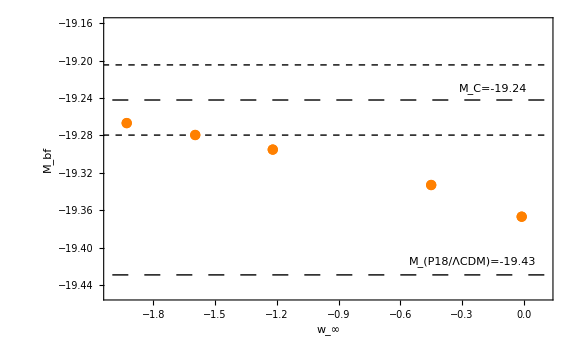

```mathematica
Mprior=−19.2421;
σMprior=0.0375;
Mplbf=-19.429;
Mbflist=Table[{{Merrwinfty[[i,1]],Around[Merrwinfty[[i,2]],{-Merrwinfty[[i,3]],Merrwinfty[[i,3]]}]}},{i,1,Length[Merrwinfty]}];
Mplt=ListPlot[Mbflist,Frame->True,PlotStyle->Orange,FrameLabel->{"w_∞","M_bf"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Large,Axes->None,PlotRange->{{0.1,-2},{-19.45,-19.16}},Epilog->{Text["M_C=-19.24",{-0.15,-19.23}],Text["M_(P18/ΛCDM)=-19.43",{-0.25,-19.415}],{Dashing[0.02],Line[{{0.1,Mprior},{-8,Mprior}}]},{Dashing[0.008],Line[{{0.1,Mprior-σMprior},{-8,Mprior-σMprior}}]},{Dashing[0.008],Line[{{0.1,Mprior+σMprior},{-8,Mprior+σMprior}}],{Dashing[0.02],Line[{{0.1,Mplbf},{-8,Mplbf}}]}}}]
```

```mathematica
Export[NotebookDirectory[]<>"Fig4.pdf",Mplt,ImageResolution->1000];
```

```mathematica
listcpldgnchi2=Table[{cpldgnchi2[[p,4]],cpldgnchi2[[p,1]]},{p,1,Length[cpldgnchi2]}];
```

```mathematica
listcpldgnchi2special={{cpldgnchi2[[28,4]],cpldgnchi2[[28,1]]},{cpldgnchi2[[79,4]],cpldgnchi2[[79,1]]},{cpldgnchi2[[101,4]],cpldgnchi2[[101,1]]},{cpldgnchi2[[91,4]],cpldgnchi2[[91,1]]},{cpldgnchi2[[51,4]],cpldgnchi2[[51,1]]}};
```

### Figure 1

0.545455

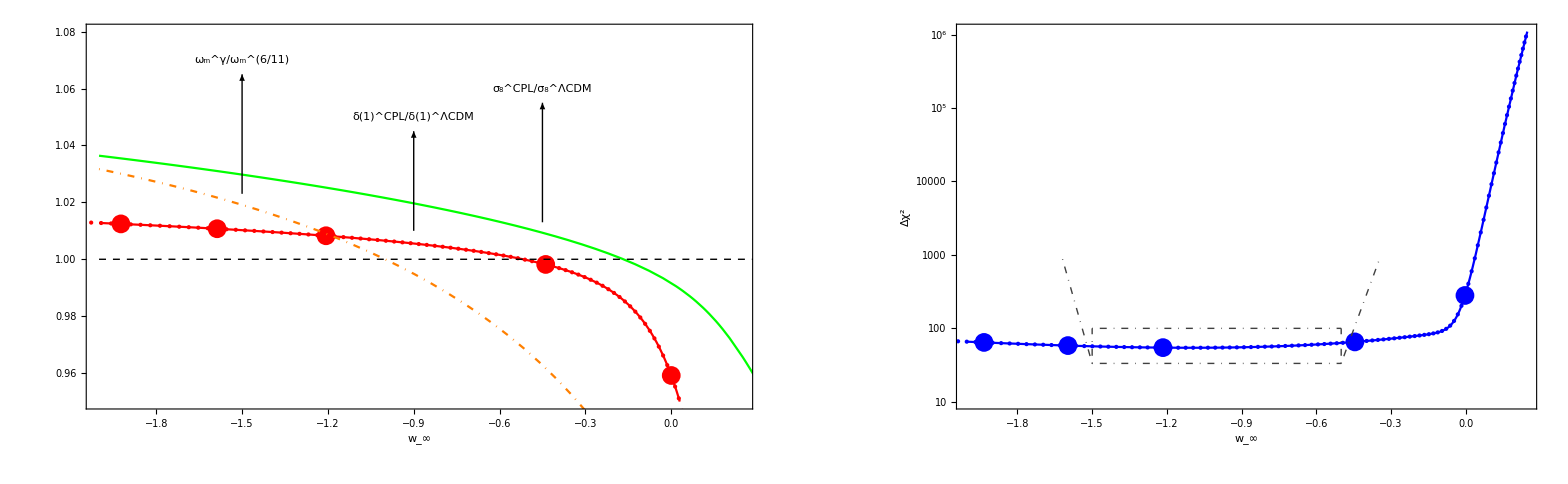

```mathematica
intlists8=Interpolation[cpls8winfty];
pltints8=Plot[intlists8[x],{x,-2,0.3}, Frame->True,FrameLabel->{"w_∞"," "},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->Green,ImageSize->900,PlotRange->{{-2,0.24},{0.95,1.15}}, FrameStyle -> Directive[Black, Thick]];
intlist1=Interpolation[listcpldgnchi2];
pltint1=LogPlot[intlist1[x],{x,-2,0.3}, Frame->True,FrameLabel->{"w_∞","Δχ^2"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotStyle->Blue,ImageSize->900,PlotRange->{{-2,0.24},{10,1100000}}, FrameStyle -> Directive[Black, Thick]];
pltcplgnchi2=ListLogPlot[listcpldgnchi2, Frame->True,FrameLabel->{"w_∞","Δχ^2"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{PointSize->Medium,Blue},ImageSize->900,PlotRange->{{-2,0.24},{10,1100000}}, FrameStyle -> Directive[Black, Thick]];
pltcplgnchi2special=ListLogPlot[listcpldgnchi2special, Frame->True,FrameLabel->{"w_∞","Δχ^2"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{PointSize->0.015,Blue},ImageSize->900,PlotRange->{{-2,0.24},{10,1100000}}, FrameStyle -> Directive[Black, Thick]];
listgrtab=Table[{grtab[[p,4]],grtab[[p,1]]},{p,1,Length[grtab]}];
listgrtabspecial={{grtab[[28,4]],grtab[[28,1]]},{grtab[[79,4]],grtab[[79,1]]},{grtab[[101,4]],grtab[[101,1]]},{grtab[[91,4]],grtab[[91,1]]},{grtab[[51,4]],grtab[[51,1]]}};
intlist2=Interpolation[listgrtab];
pltint2=Plot[intlist2[x],{x,-2,0.3}, Frame->True,FrameLabel->{"w_∞",""},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->Red,ImageSize->900,PlotRange->{{-2,0.24},{0.95,1.08}}, FrameStyle -> Directive[Black, Thick]];
pltgrtab=ListPlot[listgrtab, Frame->True,FrameLabel->{"w_∞",""},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{PointSize->Medium,Red},ImageSize->900,PlotRange->{{-2,0.24},{0.8,1.1}}, FrameStyle -> Directive[Black, Thick]];
pltgrtabspecial=ListPlot[listgrtabspecial, Frame->True,FrameLabel->{"w_∞",""},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{PointSize->0.015,Red},ImageSize->900,PlotRange->{{-2,0.24},{0.8,1.1}}, FrameStyle -> Directive[Black, Thick]];
pltint1zoom=Plot[intlist1[x],{x,-1.5,-0.5}, Frame->True,BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->Blue,ImageSize->500,PlotRange->Automatic, FrameStyle -> Directive[Black, Thick]];
gma=(6-3(1+winfa))/(11-6(1+winfa))//N;
gmlcdm=gma /. winfa->-1
omh2=0.143 ;
omgpl=Plot[omh2^gma/omh2^gmlcdm,{winfa,-2,0.7}, Frame->True,FrameLabel->{"w_∞",""},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotStyle->{Orange,DotDashed},ImageSize->900,PlotRange->{{-2,0.24},{0.8,1.2}}, FrameStyle -> Directive[Black, Thick]];
plt2=Show[pltint2,pltints8,pltgrtab,pltgrtabspecial,omgpl,Epilog->{{Dashed,Line[{{-2,1},{0.3,1}}]},Text["δ(1)^CPL/δ(1)^ΛCDM",{-0.9,1.05}],Text["ω_m^γ/ω_m^(6/11)",{-1.5,1.07}],Text["σ_8^CPL/σ_8^ΛCDM",{-0.45,1.06}],Arrowheads[Medium],Arrow[{{-1.5,1.023},{-1.5,1.065}}],Arrow[{{-0.9,1.01},{-0.9,1.045}}],Arrow[{{-0.45,1.013},{-0.45,1.055}}],BaseStyle->{Large,FontFamily->"Times",22}}];
plt1=Show[pltint1,pltcplgnchi2,pltcplgnchi2special];
pltinset=Show[pltint1zoom];
plt1full=Show[plt1,Epilog->{Inset[pltinset,Scaled[{0.44,0.65}]],DotDashed,Darker[Gray,0.5],Line[{{-1.5,3.5},{-1.62,6.8}}],Line[{{-0.5,3.5},{-0.345,6.8}}],Line[{{-1.5,3.5},{-1.5,4.6}}],Line[{{-0.5,3.5},{-0.5,4.6}}],Line[{{-1.5,3.5},{-0.5,3.5}}],Line[{{-1.5,4.6},{-0.5,4.6}}]},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large]];
cplgrowthchi2=GraphicsGrid[{{plt2,plt1full}},Spacings->0,ImageSize->1900]
```

```mathematica
Export[NotebookDirectory[]<>"Fig1.pdf",cplgrowthchi2,ImageResolution->1000];
```

```mathematica
dchi[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->1//N
nsig[dchi1_]:=FindRoot[dchi[nsig1]==dchi1,{nsig1,1}][[1,2]]
```

```mathematica
nsig[9.09]
```

3.01496